# Versuch 49

```mathematica
ClearAll["Global`*"]
```

## Einstellungen

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15]}
```

{Frame→True,Axes→False,FrameStyle→Directive[GrayLevel[0],Thickness[0.003]],ImageSize→700,FrameTicksStyle→Directive[GrayLevel[0],15]}

```mathematica
legendSettings={LabelStyle->Directive[Black,15],Method->{FrameStyle->Thickness[0.003],TicksStyle->Directive[Black,Thickness[0.003]]}};
```

## Gaussgewichtete Regression

```mathematica
gaussReg[xdata_,ydata_,dydata_]:=With[{Δ=Total[1/#^2&/@ dydata]Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[xdata]}]-(Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[xdata]}])^2},{1/Δ(Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}] Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), 1/Δ(Total[1/#^2&/@ dydata]Sum[xdata[[i]]ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]-Sum[xdata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]Sum[ydata[[i]]/dydata[[i]]^2,{i,1,Length[ydata]}]), Sqrt[1/Δ Sum[xdata[[i]]^2/dydata[[i]]^2,{i,1,Length[ydata]}]], Sqrt[1/Δ Total[1/#^2&/@ dydata]]} ]
```

## Schottky-Langmuir-Raumladungsgesetz

```mathematica
data65=Import[NotebookDirectory[]<>"Anodenstrom Uh 6.5 V.xlsx"][[1]];
```

```mathematica
data75=Import[NotebookDirectory[]<>"Anodenstrom Uh 7.5 V.xlsx"][[1]];
```

```mathematica
yerror65=ConstantArray[0.1,Length[data65]];
yerror75=ConstantArray[0.1,Length[data75]];
```

```mathematica
xerror65=ConstantArray[0.1,Length[data65]];
xerror75=ConstantArray[0.1,Length[data75]];
```

### Abb 4

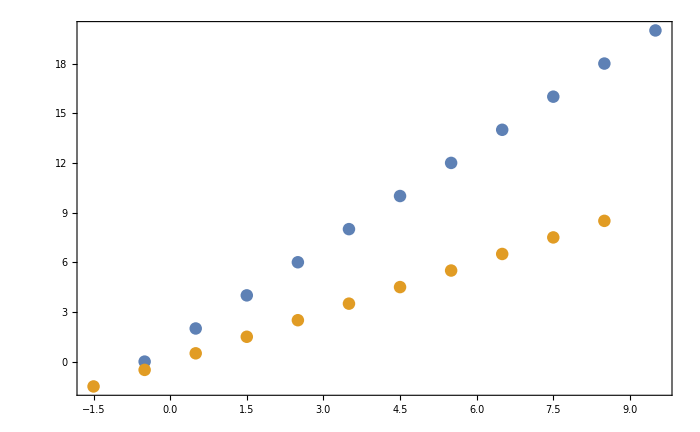

```mathematica
ListPlot[{Table[{Around[data65[[i,1]],xerror65[[i]]],Around[data65[[i,2]],yerror65[[i]]]},{i,1,Length[data65]}],Table[{Around[data75[[i,1]],xerror75[[i]]],Around[data75[[i,2]],yerror75[[i]]]},{i,1,Length[data75]}]},pltsettings]
```

### Cut The Data!!!!

```mathematica
cutData65=DeleteCases[data65,x_/;x[[1]]<0];
cutData75=DeleteCases[data75,x_/;x[[1]]<0];
```

```mathematica
cutyError65=yerror65[[-Length[cutData65];;-1]];
cutyError75=yerror75[[-Length[cutData75];;-1]];
```

```mathematica
cutxError65=xerror65[[-Length[cutData65];;-1]];
cutxError75=xerror75[[-Length[cutData75];;-1]];
```

### Abb. 5

The error in y^(2/3) is given by
Δy^(2/3)=2/3 y^(-2/3) Δy

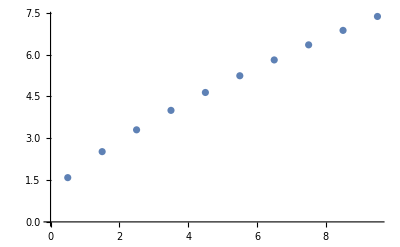

```mathematica
ListPlot[{#[[1]],#[[2]]^(2/3)}&/@cutData65]
```

```mathematica
reg1Cut=6;
```

```mathematica
pars1=gaussReg[cutData65[[1;;reg1Cut,1]],cutData65[[1;;reg1Cut,2]]^(2/3), cutyError65[[1;;reg1Cut]]]
```

{1.37725,0.723821,0.0825198,0.0239046}

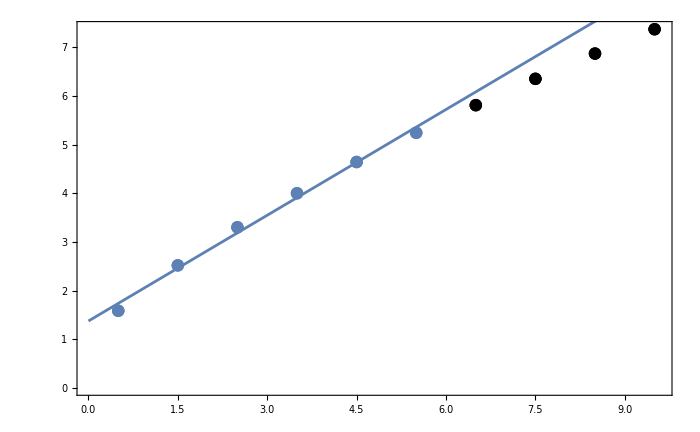

```mathematica
Show[ListPlot[Table[{{Around[cutData65⟦i,1⟧,cutxError65[[i]]],Around[cutData65⟦i,2⟧^(2/3),(2 cutyError65⟦i⟧)/(3 cutData65⟦i,2⟧^(2/3))]}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],Plot[pars1⟦1⟧+pars1⟦2⟧ x,{x,0,10}],pltsettings]
```

### Abb. 6

The error in y^(2/3) is given by
Δy^(2/3)=2/3 y^(-2/3) Δy

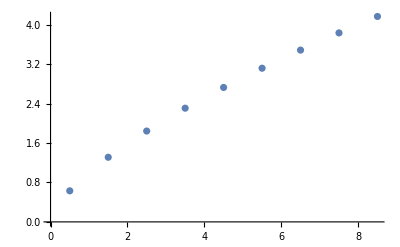

```mathematica
ListPlot[{#[[1]],#[[2]]^(2/3)}&/@cutData75]
```

```mathematica
reg2Cut=5;
```

```mathematica
pars2=gaussReg[cutData75[[1;;reg2Cut,1]],cutData75[[1;;reg2Cut,2]]^(2/3), cutyError75[[1;;reg2Cut]]]
```

{0.466077,0.518629,0.0908295,0.0316228}

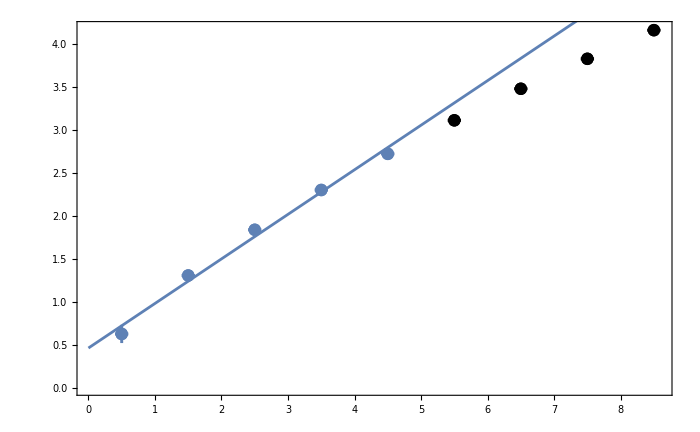

```mathematica
Show[ListPlot[Table[{{Around[cutData75⟦i,1⟧,cutxError75[[i]]],Around[cutData75⟦i,2⟧^(2/3),(2 cutyError75⟦i⟧)/(3 cutData75⟦i,2⟧^(2/3))]}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],Plot[pars2⟦1⟧+pars2⟦2⟧ x,{x,0,10}],pltsettings]
```

### Abb 7

```mathematica
logData65=Log[cutData65]
```

{{-0.693147,0.693147},{0.405465,1.38629},{0.916291,1.79176},{1.25276,2.07944},{1.50408,2.30259},{1.70475,2.48491},{1.8718,2.63906},{2.0149,2.77259},{2.14007,2.89037},{2.25129,2.99573}}

```mathematica
dlogx65=Table[cutxError65[[i]]/cutData65[[i,1]],{i,1,Length[cutData65]}];
dlogy65=Table[cutyError65[[i]]/cutData65[[i,2]],{i,1,Length[cutData65]}]
```

{0.05,0.025,0.0166667,0.0125,0.01,0.00833333,0.00714286,0.00625,0.00555556,0.005}

```mathematica
pars3=gaussReg[logData65[[1;;reg1Cut,1]],logData65[[1;;reg1Cut,2]],dlogy65[[1;;reg1Cut]]]
```

{1.07014,0.821219,0.0192887,0.0131773}

```mathematica
cutData65[[1]]
cutData65[[-1]]
```

{0.5,2.}

{9.5,20.}

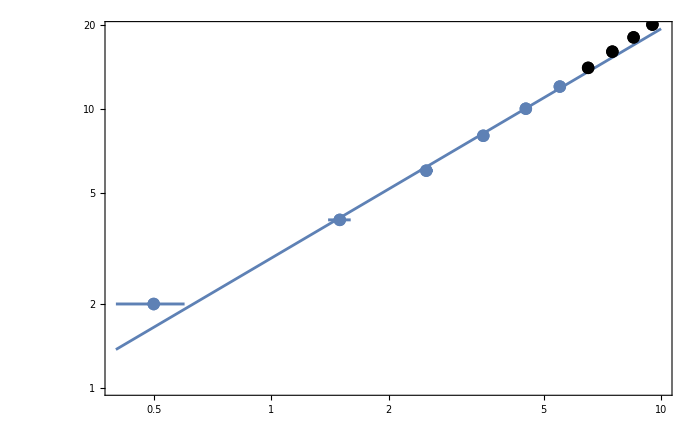

```mathematica
Show[LogLogPlot[E^pars3[[1]] x^(pars3[[2]]),{x,0.4,10}],ListLogLogPlot[Table[{{Around[cutData65⟦i,1⟧,cutxError65[[i]]],Around[cutData65⟦i,2⟧,cutyError65⟦i⟧]}},{i,1,Length[cutData65]}],PlotStyle->Table[Directive[If[i<=reg1Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData65]}]],pltsettings]
```

### Abb 8

```mathematica
logData75=Log[cutData75];
```

```mathematica
dlogx75=Table[cutxError75[[i]]/cutData75[[i,1]],{i,1,Length[cutData75]}];
dlogy75=Table[cutyError75[[i]]/cutData75[[i,2]],{i,1,Length[cutData75]}];
```

```mathematica
pars4=gaussReg[logData75[[1;;reg2Cut,1]],logData75[[1;;reg2Cut,2]],dlogy75[[1;;reg2Cut]]]
```

{0.,1.,0.0614747,0.0469325}

```mathematica
cutData75[[1]]
cutData75[[-1]]
```

{0.5,0.5}

{8.5,8.5}

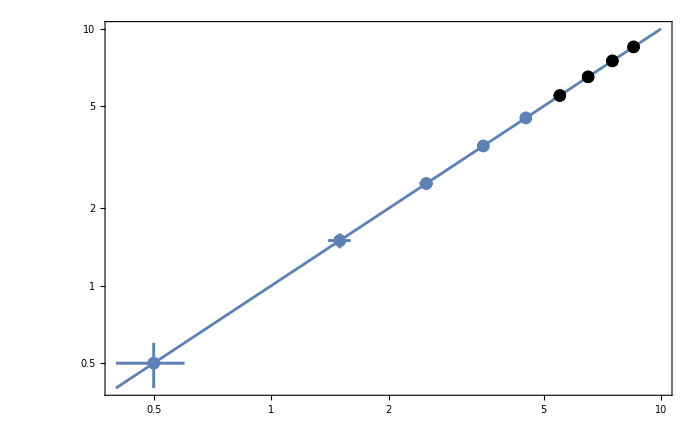

```mathematica
Show[LogLogPlot[E^pars4[[1]] x^(pars4[[2]]),{x,0.4,10}],ListLogLogPlot[Table[{{Around[cutData75⟦i,1⟧,cutxError75[[i]]],Around[cutData75⟦i,2⟧,cutyError75⟦i⟧]}},{i,1,Length[cutData75]}],PlotStyle->Table[Directive[If[i<=reg2Cut,ColorData[97,1],Black],Thickness[0.003]],{i,1,Length[cutData75]}]],pltsettings]
```

### Abb 9

```mathematica
Temp[Uh_]:=1616+97 Uh
```

```mathematica
dataTemp=Import[NotebookDirectory[]<>"Temperaturabhangigkeit.xlsx"][[1]];
```

```mathematica
ydataTemp=#[[2]]/Temp[#[[1]]]^2&/@dataTemp;
```

```mathematica
logydataTemp=Log[ydataTemp];
```

```mathematica
xdataTemp=1/(Temp/@dataTemp[[All,1]]);
```

```mathematica
fit=LinearModelFit[Transpose[{xdataTemp, logydataTemp}],x,x]
```

FittedModel[…]

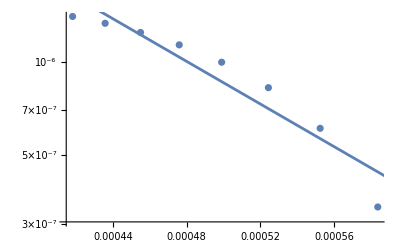

```mathematica
Show[ListLogPlot[Transpose[{xdataTemp,ydataTemp}]],LogPlot[Exp[fit[x]],{x,0,1}]]
```